Theta is the angle  describing the distortion. ThetaP and PhiP relate to the direction of r

```mathematica
ClearAll["Global`*"]
```

```mathematica
thetaS = Cos[thetaP]Cos[θ]+Sin[thetaP]Sin[θ]Cos[phiP-(2Pi*s)/3];
```

Create potential with simplifications due to threefold symmetry axis

```mathematica
VKhom = V0 + v1*Sum[LegendreP[2,thetaS],{s,1,3}]+v2*Sum[LegendreP[4,thetaS],{s,1,3}];
```

The radial part of the wave function

```mathematica
Rwave = 4/(81Sqrt[30]*a0^(3/2))*r^2/a0^2*Exp[-r/(3a0)];
```

ψ1 = xy 
ψ2 = xz
ψ3 = yz
ψ4 = x2-y2
ψ5 = 3z2-r2

```mathematica
ψ[1]=Rwave*((Sin[thetaP]^2)Sin[2phiP])/2;
ψ[2]=Rwave*Sin[thetaP]Cos[thetaP]Cos[phiP];
ψ[3]=Rwave*Sin[thetaP]Cos[thetaP]Sin[phiP];
ψ[4]=Rwave*((Sin[thetaP]^2)Cos[2phiP])/2;
ψ[5]=Rwave*((3Cos[thetaP]^2)-1)/2;
```

Matrix elements  of crystal field potential for the complete set of d functions as given by Khomskii 2015.

```mathematica
a4 = -3/2(5/2 Cos[θ]^4-15/7 Cos[θ]^2+3/14);
a2 = 27/35 κ(3Cos[θ]^2-1);
b = 3Sin[θ]^3Cos[θ];
```

```mathematica
Vab = E0{{(-3a4-10a2)/15,0,-b/2,0,0},
		{0,(12a4+5a2)/15,0,b/2,0},
		{-b/2,0,(12a4+5a2)/15,0,0},
		{0,b/2,0,(-3a4-10a2)/15,0},
		{0,0,0,0,(-18a4+10a2)/15}};
```

```mathematica
Energies = Eigenvalues[Vab]//Simplify;
E1 = Energies[[1]]/E0//FullSimplify;
E2 = Energies[[2]]/E0//FullSimplify;
E3 = Energies[[3]]/E0//FullSimplify;
E4 = Energies[[4]]/E0//FullSimplify;
E5 = Energies[[5]]/E0//FullSimplify;
```

We will later plot energy vs. theta for a range of  kappa.
Kappa depends on the crystal field coefficients v1 and v2, as well as on the radial part of the wave function for d 
electrons. Kappa varies depending on the material usually from ~0.1-1

Now we have the orbital wave functions after the trigonal distortion is applied in a trigonal crystal field. We start with the
eg sigma orbitals. These wave functions are not used in this code for anything, but I wanted to have them typed up somewhere.

```mathematica
d1 = Sin[α/2]ψ[4]-Cos[α/2]ψ[2];
d2 = Sin[α/2]ψ[4]+Cos[α/2]ψ[2];
e1 =-Sin[α/2]ψ[1]-Cos[α/2]ψ[3];
e2 =-Sin[α/2]ψ[1]+Cos[α/2]ψ[3];
```

Next come the t2g. a1g is same for cation 1 and 2

```mathematica
a1g = ψ[5];
b1 = -Cos[α/2]ψ[1]+Sin[α/2]ψ[3];
b2 = -Cos[α/2]ψ[1]-Sin[α/2]ψ[3];
c1 = Cos[α/2]ψ[4]+Sin[α/2]ψ[2];
c2 = Cos[α/2]ψ[4]-Sin[α/2]ψ[2];
```

Now we solve for alpha neglecting effect of neighboring metal atoms in the chain

```mathematica
α = ArcCos[(a2+a4)/Sqrt[(a2+a4)^2+b^2]];
```

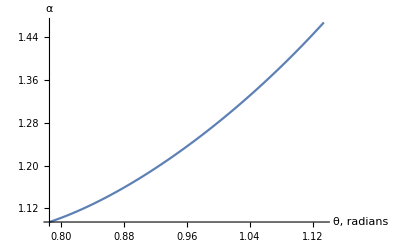

```mathematica
Plot[Evaluate[α/.κ->0.1], {θ,0.785,1.134},AxesLabel->{"θ, radians","α"}]
```

Only need 3 energies because there are two doublets

```mathematica
Energy = {E1, E2, E5};
```

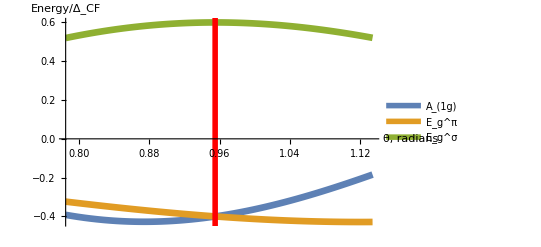

```mathematica
Plot[Evaluate[Energy/.κ->0.1],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->{StyleBox[SubscriptBox["A","1g"], FontSize->30]//DisplayForm,StyleBox[SubsuperscriptBox["E","g","π"], FontSize->30]//DisplayForm,StyleBox[SubsuperscriptBox["E","g","σ"],FontSize->30]//DisplayForm},AxesLabel->{"θ, radians","Energy/Δ_CF"}, BaseStyle->{FontSize->30}]
```

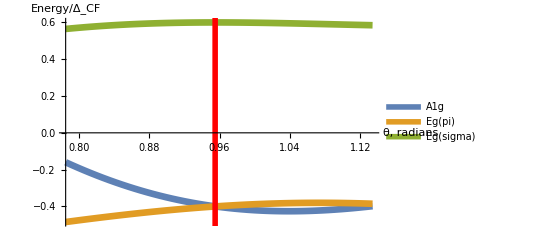

```mathematica
Plot[Evaluate[Energy/.κ->1],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->{"A1g","Eg(pi)","Eg(sigma)"},AxesLabel->{"θ, radians","Energy/Δ_CF"}]
```

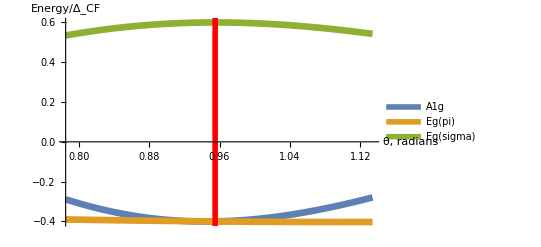

```mathematica
Plot[Evaluate[Energy/.κ->0.5],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->{"A1g","Eg(pi)","Eg(sigma)"},AxesLabel->{"θ, radians","Energy/Δ_CF"}]
```

We now consider the effect of neighboring metal atoms

```mathematica
a2 = 27/35 κ(3Cos[θ]^2-1)-(27κ)/35 Z/(12Cos[θ]^2);
Vab = E0{{(-3a4-10a2)/15,0,-b/2,0,0},
		{0,(12a4+5a2)/15,0,b/2,0},
		{-b/2,0,(12a4+5a2)/15,0,0},
		{0,b/2,0,(-3a4-10a2)/15,0},
		{0,0,0,0,(-18a4+10a2)/15}};
Energies = Eigenvalues[Vab]//Simplify;
E1 = Energies[[1]]/E0//FullSimplify;
E2 = Energies[[2]]/E0//FullSimplify;
E3 = Energies[[3]]/E0//FullSimplify;
E4 = Energies[[4]]/E0//FullSimplify;
E5 = Energies[[5]]/E0//FullSimplify;
α = ArcCos[(a2+a4)/Sqrt[(a2+a4)^2+b^2]];
Energy = {E1, E2, E5};
```

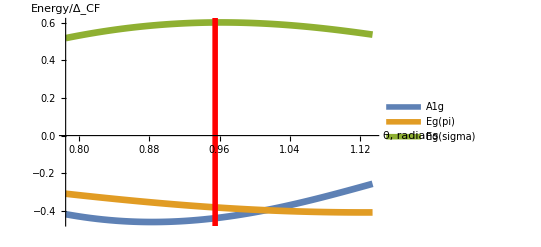

```mathematica
Plot[Evaluate[Energy/.{κ->0.1,Z->3}],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->{"A1g","Eg(pi)","Eg(sigma)"},AxesLabel->{"θ, radians","Energy/Δ_CF"}]
```

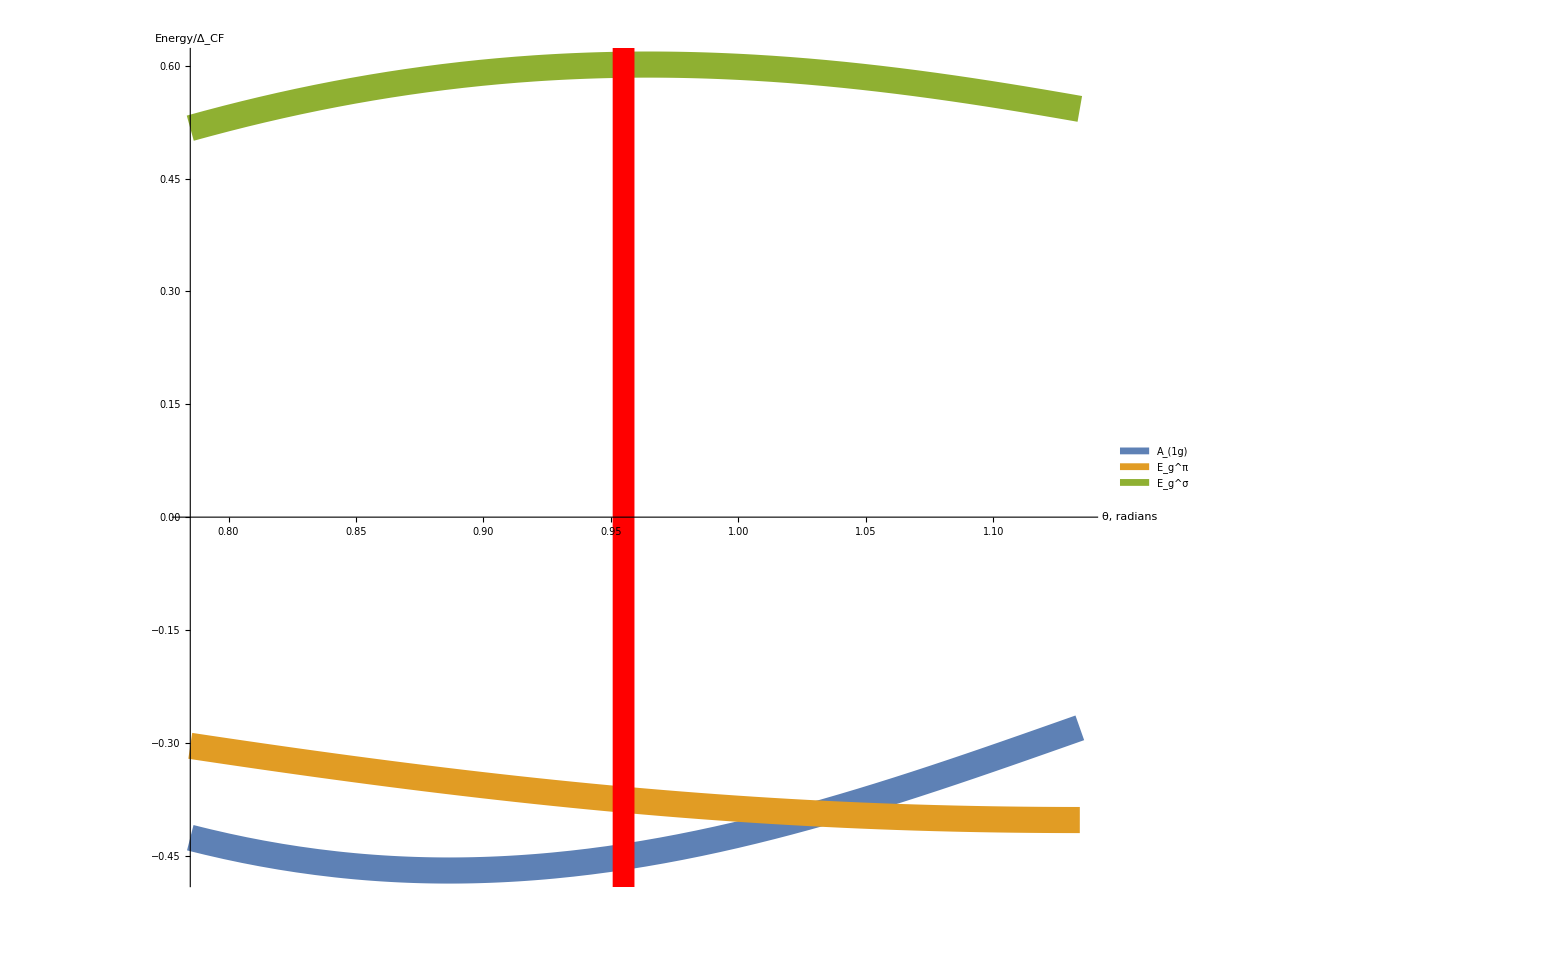

```mathematica
Plot[Evaluate[Energy/.{κ->0.1,Z->4}],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->SwatchLegend[{StyleBox[SubscriptBox["A","1g"], FontSize->60 ]//DisplayForm,StyleBox[SubsuperscriptBox["E","g","π"], FontSize->60]//DisplayForm,StyleBox[SubsuperscriptBox["E","g","σ"],FontSize->60]//DisplayForm},LegendMarkerSize->20],AxesLabel->{Style["θ, radians", FontSize->60],Style["Energy/Δ_CF", FontSize->60]}, BaseStyle->{FontSize->60}, ImageSize->1600]
```

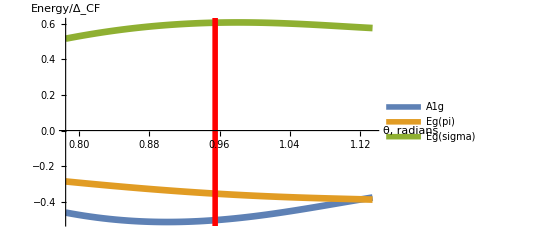

```mathematica
Plot[Evaluate[Energy/.{κ->0.1,Z->8}],{θ,0.785,1.134}, PlotStyle->{Thickness[0.012]}, GridLines->{{0.955},None},GridLinesStyle->Directive[Red, Thickness[0.01]],
PlotLegends->{"A1g","Eg(pi)","Eg(sigma)"},AxesLabel->{"θ, radians","Energy/Δ_CF"}, BaseStyle->{FontSize->24}]
```

Time to plot wavefunctions without trigonal distortion. First change variables to more recognizable spherical coordinates. Theta here 
is not the angle characterizing the trigonal distortion but rather the angle in the x-y plane. d1 and e1 are
eg sigma  orbitals while the a1g, b1, and c1 comprise the t2g.

```mathematica
funtime1 = d1/.{a0->1,α->ArcCos[1/Sqrt[3]],thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime2 = e1/.{a0->1,α->ArcCos[1/Sqrt[3]],thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime3 = a1g/.{a0->1,α->ArcCos[1/Sqrt[3]],thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime4 = b1/.{a0->1,α->ArcCos[1/Sqrt[3]],thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime5 = c1/.{a0->1,α->ArcCos[1/Sqrt[3]],thetaP-> θ,phiP-> ϕ}//FullSimplify;
```

Convert to Cartesian coordinates for plotting.

```mathematica
newfun1= TransformedField["Spherical"->"Cartesian",funtime1,{r,θ,ϕ}-> {x, y, z}];
newfun2= TransformedField["Spherical"->"Cartesian",funtime2,{r,θ,ϕ}-> {x, y, z}];
newfun3= TransformedField["Spherical"->"Cartesian",funtime3,{r,θ,ϕ}-> {x, y, z}];
newfun4= TransformedField["Spherical"->"Cartesian",funtime4,{r,θ,ϕ}-> {x, y, z}];
newfun5= TransformedField["Spherical"->"Cartesian",funtime5,{r,θ,ϕ}-> {x, y, z}];
```

```mathematica
DensityPlot3D[newfun1,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

```mathematica
DensityPlot3D[newfun2,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
DensityPlot3D[newfun3,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
DensityPlot3D[newfun4,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
DensityPlot3D[newfun5,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Now we plot with finite alpha  where range can be from 0 to pi.

```mathematica
var = 0;
funtime1 = d1/.{a0->1,α->var,thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime2 = e1/.{a0->1,α->var,thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime3 = a1g/.{a0->1,α->var,thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime4 = b1/.{a0->1,α->var,thetaP-> θ,phiP-> ϕ}//FullSimplify;
funtime5 = c1/.{a0->1,α->var,thetaP-> θ,phiP-> ϕ}//FullSimplify;
newfun1= TransformedField["Spherical"->"Cartesian",funtime1,{r,θ,ϕ}-> {x, y, z}];
newfun2= TransformedField["Spherical"->"Cartesian",funtime2,{r,θ,ϕ}-> {x, y, z}];
newfun3= TransformedField["Spherical"->"Cartesian",funtime3,{r,θ,ϕ}-> {x, y, z}];
newfun4= TransformedField["Spherical"->"Cartesian",funtime4,{r,θ,ϕ}-> {x, y, z}];
newfun5= TransformedField["Spherical"->"Cartesian",funtime5,{r,θ,ϕ}-> {x, y, z}];
DensityPlot3D[newfun1,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
DensityPlot3D[newfun2,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
DensityPlot3D[newfun3,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
DensityPlot3D[newfun4,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
DensityPlot3D[newfun5,{x, -15, 15}, {y, -15, 15},{z, -15, 15},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»